```mathematica
expr=f[x] - (a0+a1(x-a)+a2(x-a)^2+a3(x-a)^3)==0
```

-a0-a1 (-a+x)-a2 (-a+x)^2-a3 (-a+x)^3+f[x]==0

```mathematica
expr/. x->a
```

-a0+f[a]==0

```mathematica
expr=expr /. a0->f[a]
```

-a1 (-a+x)-a2 (-a+x)^2-a3 (-a+x)^3-f[a]+f[x]==0

```mathematica
expr=-a1 -a2 (-a+x)-a3 (-a+x)^2+(-f[a]+f[x])/(x-a)
```

-a1-a2 (-a+x)-a3 (-a+x)^2+(-f[a]+f[x])/(-a+x)

```mathematica
((-a1 (-a+x)-a2 (-a+x)^2-a3 (-a+x)^3-f[a]+f[x]==0)/(-a+x))
```

```mathematica
a1=f'[a]
```

```mathematica
an = f^(n)(a)/n!
```

(a f^n)/(n!)

```mathematica
Series[Exp[x], {x, 0, 5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

```mathematica
TraditionalForm[%]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O(x^6)

```mathematica
(*0*)
```

```mathematica
sol = Solve[{D[x*Sin[x]]==0, x≥0, x≤π/2},x]
```

{{x→0},{x→0}}

```mathematica
x/.sol
```

{0,0}

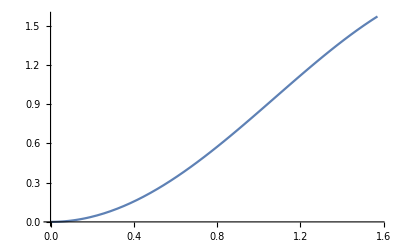

```mathematica
Plot[x*Sin[x],{x, 0, π/2}]
```

```mathematica
(*делаем вывод, что минимум достигается на левом конце отрезка в точке 0*)
```

```mathematica
(*1*)
pol = Table[RandomReal[{-5,5}] x^n,{n, 10}]//Total
```

2.93752 x+0.413711 x^2+3.59475 x^3-4.51853 x^4+3.0494 x^5-2.73523 x^6-3.26513 x^7+3.47136 x^8-3.81228 x^9-4.96803 x^10

```mathematica
sol1= Solve[pol==0,x]
```

{{x→-1.30506-0.352218 ⅈ},{x→-1.30506+0.352218 ⅈ},{x→-0.338168-0.581891 ⅈ},{x→-0.338168+0.581891 ⅈ},{x→0.},{x→0.0972584-0.883311 ⅈ},{x→0.0972584+0.883311 ⅈ},{x→0.716925-0.708269 ⅈ},{x→0.716925+0.708269 ⅈ},{x→0.890736}}

```mathematica
x/.sol1
```

{-1.30506-0.352218 ⅈ,-1.30506+0.352218 ⅈ,-0.338168-0.581891 ⅈ,-0.338168+0.581891 ⅈ,0.,0.0972584-0.883311 ⅈ,0.0972584+0.883311 ⅈ,0.716925-0.708269 ⅈ,0.716925+0.708269 ⅈ,0.890736}

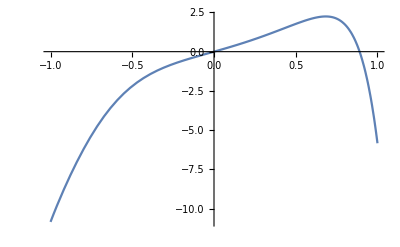

```mathematica
pl1=Plot[pol, {x, -1,1}];
```

```mathematica
pl2=ListPlot[{{0,0},{0.8907360032115719,0}}, PlotStyle->Red];
```

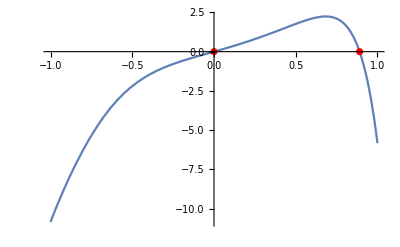

```mathematica
Show[pl1, pl2]
```

```mathematica
(*2*)
```

```mathematica
Clear[sol2]
```

```mathematica
sol2 = Solve[{Sin[x]==Cos[x]}]
```

{{x→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π/4+2 π C[1],C[1]∈ℤ]}}

```mathematica
points = Table[C[1]->i,{i,-15,15}];
pointList = Table[sol2/.points[[i]], {i, 30}];
```

```mathematica
pl3=Plot[Sin[x], {x,-15π, 15π}];
```

```mathematica
pl4 = Plot[Cos[x], {x,-15π, 15π}, PlotStyle->Green];
```

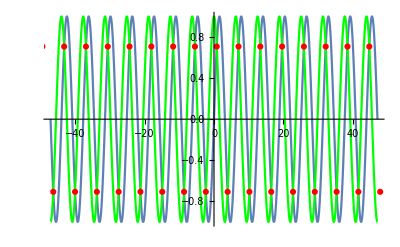

```mathematica
Show[pl3,pl4,ListPlot[{x, Cos[x]}/.pointList, PlotStyle->Red]]
```

```mathematica
(*часть 2*)
```

```mathematica
TaylorPlot[f_,{a_,b_},point_,n_]:={Plot[{f[x], Evaluate[Normal[Series[f[x],{x,point,n}]]]},{x,a,b},PlotStyle->{Red,Blue},PlotLegends->{"f(x)","Taylor"}],TraditionalForm[Series[f[x],{x,point,n}]]}
```

```mathematica
(*1*)
```

```mathematica
func[x_]:=Cos[x+x^2]
```

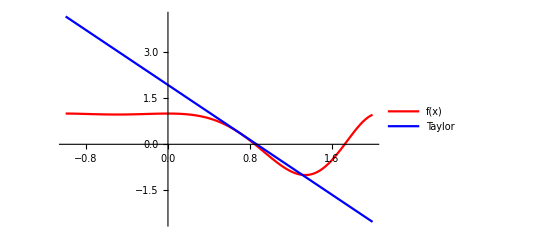
{-Graphics-,0.37166-2.22809 (x-0.7)+O((x-0.7)^2)}

```mathematica
TaylorPlot[func[#]&, {-1,2},0.7,1]
```

```mathematica
(*приближение хорошее от 0.5 до 1.35*)
```

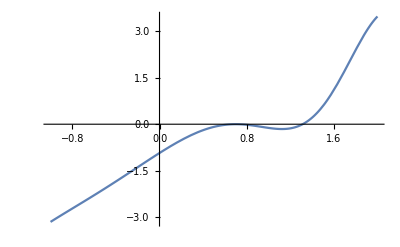

```mathematica
Plot[func[x]-0.37166 + 2.22809(x-0.7),{x,-1,2}]
```

```mathematica
(*погрешность по модулю меньше 1 на интервале от 0 до примерно 1.5, далее начинает расти*)
```

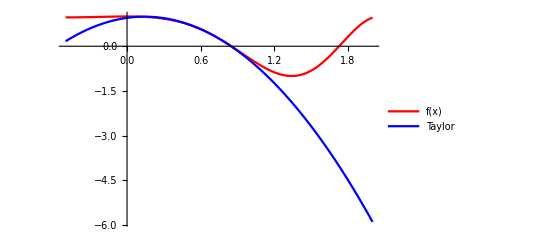
{-Graphics-,0.37166-2.22809 (x-0.7)-1.99875 (x-0.7)^2+O((x-0.7)^3)}

```mathematica
TaylorPlot[func[#]&, {-0.5,2},0.7,2]
```

```mathematica
(*приближение хорошее от 0 до 1*)
```

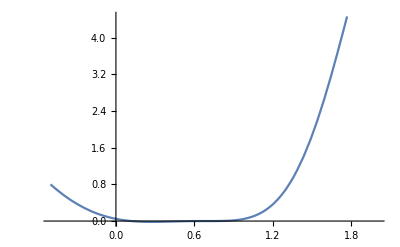

```mathematica
Plot[func[x]-0.37166 + 2.22809(x-0.7)+1.99875(x-0.7)^2, {x, -0.5, 2}]
```

```mathematica
(*погрешность почти равна 0 на интервале от 0 до 1, далее начинает возрастать, больше 1 при х больше примерно 1.5*)
```

```mathematica
(*как и ожидалось, многочлен Тейлора большего порядка более точно приближен к функции*)
```

```mathematica
(*2*)
```

```mathematica
diff = Cos[π/3]+Cos'[π/3](x-π/3)
```

1/2-1/2 √3 (-π/3+x)

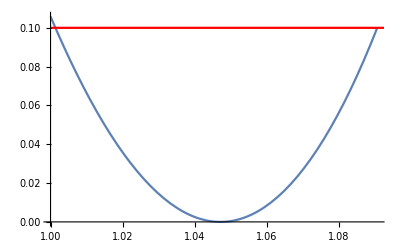

```mathematica
Show[Plot[Abs[Cos[x] - diff]*100/Cos[x],{x,1,1.0908}], Plot[0.1, {x,1,1.12}, PlotStyle->Red]]
```

```mathematica
FindRoot[(Abs[Cos[x]-diff] *100)/Cos[x]==0.1,{x,1.05,1.3}]
FindRoot[(Abs[Cos[x]-diff] *100)/Cos[x]==0.1,{x,1,1.06}]
```

{x→1.09073}

{x→1.00136}

```mathematica
(*косинус можно вычислять в окрестности данной точки с требуемой точностью на отрезке от 1.0013565345676725 до 1.0907323189710576*)
```

```mathematica
(*3*)
```

```mathematica
taylor=Series[Cos[x], {x, π/3, 2}]//Normal
```

1/2-1/2 √3 (-π/3+x)-1/4 (-π/3+x)^2

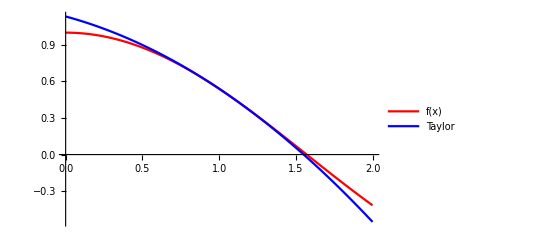
{-Graphics-,1/2-1/2 √3 (x-π/3)-1/4 (x-π/3)^2+O((x-π/3)^3)}

```mathematica
TaylorPlot[Cos[#]&,{0,2},π/3,2 ]
```

```mathematica
pl = Plot[Abs[Cos[x] - 1/2+1/2Sqrt[3](x-π/3)+1/4(x-π/3)^2]*100/Cos[x],{x,0.88,1.2} ];
```

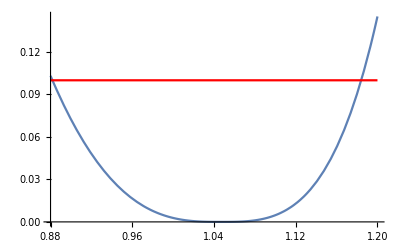

```mathematica
Show[pl,Plot[0.1,{x,0.88,1.2},PlotStyle->Red]]
```

```mathematica
FindRoot[(Abs[Cos[x]- 1/2+1/2Sqrt[3](x-π/3)+1/4(x-π/3)^2] *100)/Cos[x]==0.1,{x,0.8,1}]
```

{x→0.88188}

```mathematica
FindRoot[(Abs[Cos[x]- 1/2+1/2Sqrt[3](x-π/3)+1/4(x-π/3)^2] *100)/Cos[x]==0.1,{x,1.15,1.2}]
```

{x→1.18408}

```mathematica
(*можно вычислять косинус таким образом на отрезке от 0.8818795147610579 до 1.1840798143937759*)
```

```mathematica
(*4*)
```

```mathematica
func[x_]:= x*Tan[x]
```

```mathematica
diff2= func[π/4]+func'[π/4](x-π/4)
```

π/4+(1+π/2) (-π/4+x)

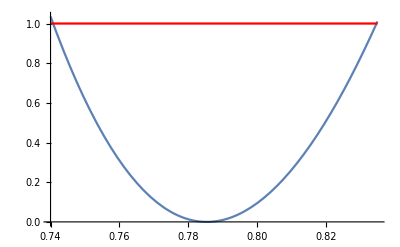

```mathematica
Show[Plot[Abs[func[x] - diff2]*100/func[x],{x,0.74,0.835}], Plot[1, {x,0.74,0.835}, PlotStyle->Red]]
```

```mathematica
FindRoot[(Abs[func[x] - diff2]*100/func[x])==1,{x,0.6,0.78}]
```

{x→0.740749}

```mathematica
FindRoot[(Abs[func[x] - diff2]*100/func[x])==1,{x,0.8,0.9}]
```

{x→0.834728}

```mathematica
(*требуемая точность достигается на интервале от 0.7407493381286329 до 0.8347283606624575*)
```

```mathematica
(*5*)
```

```mathematica
taylor1=Series[Log[x+1], {x, 0, 1}]//Normal;
```

```mathematica
taylor2=Series[Log[x+1], {x, 0, 2}]//Normal;
```

```mathematica
taylor1/.x->0.1
```

0.1

```mathematica
taylor2/.x->0.1
```

0.095

```mathematica
Log[1.1]
```

0.0953102

```mathematica
(Abs[Log[1.1] - taylor1/.x->0.1]*100/Log[1.1])≤0.5
```

False

```mathematica
(Abs[Log[1.1] - taylor2/.x->0.1]*100/Log[1.1])<=0.5
```

True

```mathematica
(*для требуемой точности можно брать многочлен Тейлора второй степени и выше*)
```

```mathematica
(*6*)
```

```mathematica
Clear[taylor4]
```

```mathematica
taylor3=Series[ArcTan[x], {x, 0, 2}]//Normal;
```

```mathematica
taylor3/.x->0.2
```

0.2

```mathematica
taylor4=Series[ArcTan[x], {x, 0, 3}]//Normal;
```

```mathematica
taylor4/.x->0.2
```

0.197333

```mathematica
ArcTan[0.2]
```

0.197396

```mathematica
(Abs[ArcTan[0.2] - taylor3/.x->0.2]*100/ArcTan[0.2])≤0.1
```

False

```mathematica
(Abs[ArcTan[0.2] - taylor4/.x->0.2]*100/ArcTan[0.2])≤0.1
```

True

```mathematica
(*для данной точности можно использовать многочлен Тейлора порядка 3 и выше*)
```